```mathematica
sF = 1/20 ;
```

```mathematica
ψ[x_,y_]:= Sin[Log[((x*sF)^2+(y*sF)^2)]]
```

```mathematica
Plot3D[ψ[x,y],{x,-50,50},{y,-50,50},PlotPoints->44,MaxRecursion->2]
```

-Graphics3D-

```mathematica
Plot3D[Sin[Log[((x-5)^2+(y-5)^2)]],{x,0,10},{y,0,10},PlotPoints->63,MaxRecursion->2]
```

-Graphics3D-

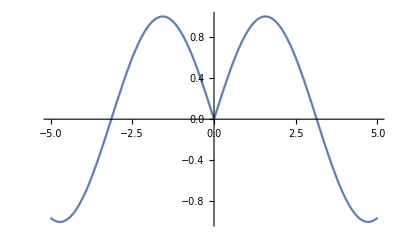

```mathematica
Plot[Sin[Sqrt[x^2]], {x, -5, 5}]
```

```mathematica
Show[%85,Boxed->False]
```

```mathematica
Sin[Log[((5-5)^2+(5-5)^2)]]
```

Interval[{-1,1}]

```mathematica
Plot3D[(Sin[Sqrt[((x)^2+(y)^2)]]),{x,-10,10},{y,-10,10},PlotPoints->63,MaxRecursion->2]
```

-Graphics3D-

```mathematica
Plot3D[(Sin[Pi*(x^2+y^2)])/(Pi*(x^2+y^2)), {x, -5, 5}, {y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[1/250*π (x^2+y^2)^0.5]/(1/250*π (x^2+y^2)^0.5),{x,-50,50},{y,-50,50},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
scalingFactor == 25;
Plot3D[Sin[1/scalingFactor*π (x^2+y^2)^0.5]/(1/scalinfFactor*π (x^2+y^2)^0.5),{x,-50,50},{y,-50,50},Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

```mathematica
scalingFactor
```

25

```mathematica
Manipulate[Plot3D[Exp[(Sin[1/dampener*π (x^2+y^2)^0.5]/(1/dampener*π (x^2+y^2)^0.5)*scalingFactor)],{x,-50,50},{y,-50,50}],{scalingFactor, 0, 2}, {dampener, 25, 34}]
```

```mathematica
Manipulate[Plot3D[(Sin[1/dampener*π *Sqrt[(x^2+y^2)]]/(1/dampener*π *Sqrt[(x^2+y^2)])),{x,-50,50},{y,-50,50}],{scalingFactor, 0, 2}, {dampener, 15, 30}]
```